# Schrödinger Equation with Absolute Value Potential

```mathematica
ClearAll["Global`*"]
```

Our Schödinger Equation has an absolute value potential, where the Hilbert Space is L^2(ℝ).

```mathematica
-ℏ^2/(2m)D[ψ[x],{x,2}]+α Abs[x]ψ[x]
```

α Abs[x] ψ[x]-(ℏ^2 ψ''[x])/(2 m)

where α is a proportionality constant to make the units consistent.

To tackle this, we can solve for the solution separately on x < 0 and x > 0, then require continuity at x = 0 to stitch the two together.

```mathematica
SE = -ℏ^2/(2m)D[ψ[x],{x,2}]+m g x ψ[x]
DSolve[SE==ψ[x],ψ[x],x]
```

g m x ψ[x]-(ℏ^2 ψ''[x])/(2 m)

{{ψ[x]→AiryAi[(-(2 m)/ℏ^2+(2 g m^2 x)/ℏ^2)/(2^(2/3) ((g m^2)/ℏ^2)^(2/3))] C[1]+AiryBi[(-(2 m)/ℏ^2+(2 g m^2 x)/ℏ^2)/(2^(2/3) ((g m^2)/ℏ^2)^(2/3))] C[2]}}

```mathematica
SE = -ℏ^2/(2m)D[ψ[x],{x,2}]-m g x ψ[x]
DSolve[SE==ψ[x],ψ[x],x]
```

-g m x ψ[x]-(ℏ^2 ψ''[x])/(2 m)

{{ψ[x]→AiryAi[(-(2 m)/ℏ^2-(2 g m^2 x)/ℏ^2)/(2^(2/3) (-(g m^2)/ℏ^2)^(2/3))] C[1]+AiryBi[(-(2 m)/ℏ^2-(2 g m^2 x)/ℏ^2)/(2^(2/3) (-(g m^2)/ℏ^2)^(2/3))] C[2]}}

The AiryBi part of both solutions blow up as x tends to infinity in the respective direction. So we throw those out. A simple stitch (and setting all constants to 1) gives

```mathematica
ψ[x_]:=Piecewise[{{AiryAi[-1-x],x<0},{AiryAi[-1+x],x>0}}]
```

This wave function is perfectly normalizable

```mathematica
A = NIntegrate[ψ[x]^2,{x,-Infinity,Infinity}]
NIntegrate[ψ[x]^2/A,{x,-Infinity,Infinity}]
```

0.573857

1.

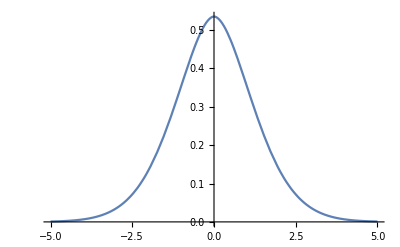

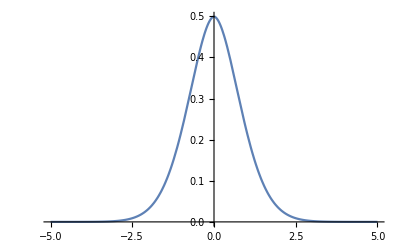

```mathematica
Plot[ψ[x],{x,-5,5}]
Plot[ψ[x]^2/A,{x,-5,5}]
```